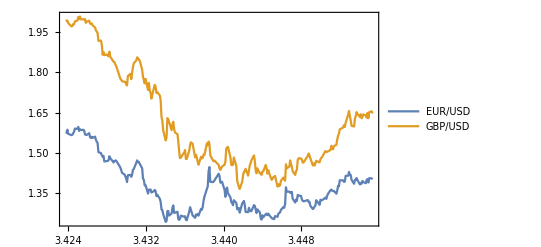

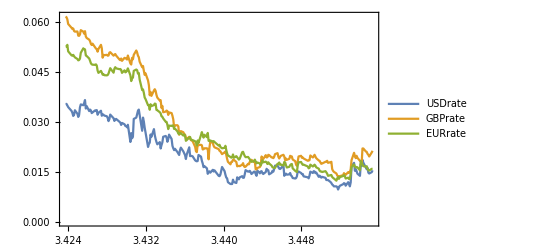

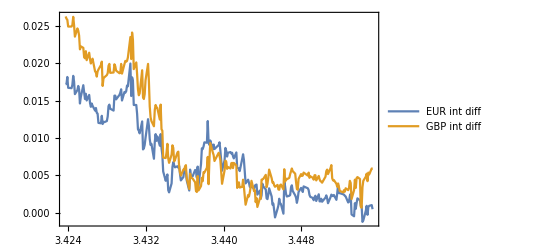

```mathematica
EURUSD=Import["/Users/wanghaibiao/Desktop/08-09 D&K model.xlsx",{"Data",1,Table[i,{i,2,251}],{1,5}}];
eurusd=Import["/Users/wanghaibiao/Desktop/08-09 D&K model.xlsx",{"Data",1,Table[i,{i,2,251}],5}];
GBPUSD=Import["/Users/wanghaibiao/Desktop/08-09 D&K model.xlsx",{"Data",1,Table[i,{i,2,251}],{1,6}}];
gbpusd=Import["/Users/wanghaibiao/Desktop/08-09 D&K model.xlsx",{"Data",1,Table[i,{i,2,251}],6}];
USDrate=Import["/Users/wanghaibiao/Desktop/08-09 D&K model.xlsx",{"Data",1,Table[i,{i,2,251}],{1,4}}];
usdrate=Import["/Users/wanghaibiao/Desktop/08-09 D&K model.xlsx",{"Data",1,Table[i,{i,2,251}],4}];
GBPrate=Import["/Users/wanghaibiao/Desktop/08-09 D&K model.xlsx",{"Data",1,Table[i,{i,2,251}],{1,3}}];
gbprate=Import["/Users/wanghaibiao/Desktop/08-09 D&K model.xlsx",{"Data",1,Table[i,{i,2,251}],3}];
EURrate=Import["/Users/wanghaibiao/Desktop/08-09 D&K model.xlsx",{"Data",1,Table[i,{i,2,251}],{1,2}}];
eurrate=Import["/Users/wanghaibiao/Desktop/08-09 D&K model.xlsx",{"Data",1,Table[i,{i,2,251}],2}];
date=Import["/Users/wanghaibiao/Desktop/08-09 D&K model.xlsx",{"Data",1,Table[i,{i,2,251}],1}];
gbpdiff=gbprate-usdrate;
eurdiff=eurrate-usdrate;
GBPdiff=Table[{date[[i]],gbpdiff[[i]]},{i,1,250}];
EURdiff=Table[{date[[i]],eurdiff[[i]]},{i,1,250}];
DateListPlot[{EURUSD,GBPUSD},PlotLegends->{"EUR/USD","GBP/USD"}]
DateListPlot[{USDrate,GBPrate,EURrate},PlotLegends->{"USDrate","GBPrate","EURrate"}]
DateListPlot[{EURdiff,GBPdiff},PlotLegends->{"EUR int diff","GBP int diff"}]
```

data input, from 2008/06/30 to 2009/06/30, exchange rate of EUR/USD & GBP/USD, interest rate of USD, GBP, EUR, interest rate differential of EUR & GBP.

Take log return of exchange rate of EUR/USD & GBP/USD, and 1-month moving average of exchange rates.

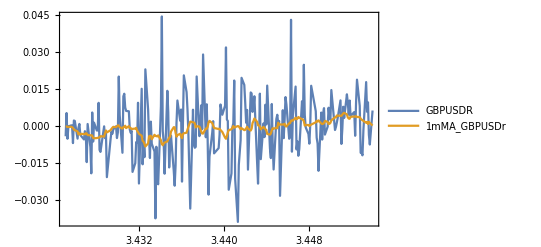

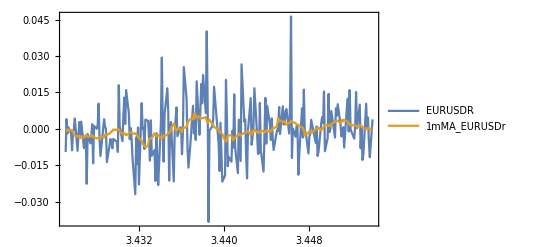

```mathematica
gbpusdr=Differences[Log[gbpusd]];
eurusdr=Differences[Log[eurusd]];
GBPUSDr=Table[{date[[i+10]],gbpusdr[[i+10]]},{i,1,229}];EURUSDr=Table[{date[[i+10]],eurusdr[[i+10]]},{i,1,229}];
mMAgbpusdr=MovingAverage[gbpusdr,21];
mMAeurusdr=MovingAverage[eurusdr,21];
mMAGBPUSDr=Table[{date[[i+10]],mMAgbpusdr[[i]]},{i,1,229}];mMAEURUSDr=Table[{date[[i+10]],mMAeurusdr[[i]]},{i,1,229}];
DateListPlot[{GBPUSDr,mMAGBPUSDr},PlotRange->All,PlotLegends->{"GBPUSDR","1mMA_GBPUSDr"}]
DateListPlot[{EURUSDr,mMAEURUSDr},PlotRange->All,PlotLegends->{"EURUSDR","1mMA_EURUSDr"}]
```

Minus the moving average, obtain the detrended log return of exchange rates

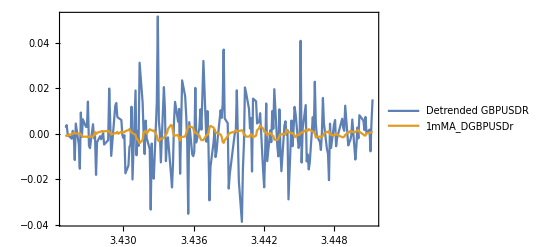

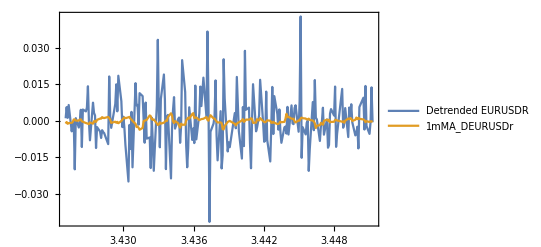

```mathematica
Dgbpusdr= Take[Drop[gbpusdr,10],229]-mMAgbpusdr;
Deurusdr= Take[Drop[eurusdr,10],229]-mMAeurusdr;
DGBPUSDr=Table[{date[[i+10]],Dgbpusdr[[i+10]]},{i,1,208}];
DEURUSDr=Table[{date[[i+10]],Deurusdr[[i+10]]},{i,1,208}];
mMADgbpusdr=MovingAverage[Dgbpusdr,21];
mMADeurusdr=MovingAverage[Deurusdr,21];
mMADGBPUSDr=Table[{date[[i+10]],mMADgbpusdr[[i]]},{i,1,208}];mMADEURUSDr=Table[{date[[i+10]],mMADeurusdr[[i]]},{i,1,208}];
DateListPlot[{DGBPUSDr,mMADGBPUSDr},PlotRange->All,PlotLegends->{"Detrended GBPUSDR","1mMA_DGBPUSDr"}]
DateListPlot[{DEURUSDr,mMADEURUSDr},PlotRange->All,PlotLegends->{"Detrended EURUSDR","1mMA_DEURUSDr"}]
```

Follow the methodology, obtain the b_t of the interest rate differentials, and k for the parameters estimation of drift component.

```mathematica
For[t=1,t≤230,t++,
Subscript[gbpdiff, t]=Take[Drop[gbpdiff,t-1],21];
Subscript[eurdiff, t]=Take[Drop[eurdiff,t-1],21];
Subscript[lm1, t]=LinearModelFit[Subscript[gbpdiff, t],x,x];
Subscript[lm2, t]=LinearModelFit[Subscript[eurdiff, t],x,x];
Subscript[b1, t]=Subscript[lm1, t]["BestFitParameters"][[2]];
Subscript[b2, t]=Subscript[lm2, t]["BestFitParameters"][[2]]];
b1=Table[Subscript[b1, t],{t,1,230}];
b2=Table[Subscript[b2, t],{t,1,230}];
empb1=EmpiricalDistribution[b1];
empb2=EmpiricalDistribution[b2];
empMAr1=EmpiricalDistribution[mMAgbpusdr];
empMAr2=EmpiricalDistribution[mMAeurusdr];
k1=Minimize[{Abs[(Quantile[empMAr1,0.975]-Quantile[empMAr1,0.025])-x*(Quantile[empb1,0.975]-Quantile[empb1,0.025])],x>0},x];
k2=Minimize[{Abs[(Quantile[empMAr2,0.975]-Quantile[empMAr2,0.025])-x*(Quantile[empb2,0.975]-Quantile[empb2,0.025])],x>0},x];
Print[k1[[2]]]
Print[k2[[2]]]
```

{x→17.3068}

{x→13.3871}

Detrended log return of exchange rates are exchange rates minus the drift component.

```mathematica
Subscript[k, 1]=17.306776802987283;
Subscript[k, 2]=13.387108877705137;
```

```mathematica
msf1=Subscript[k, 1]*b1;
msf2=Subscript[k, 2]*b2;
Mgbpusdr=Take[Drop[gbpusdr,10],230];
Meurusdr=Take[Drop[eurusdr,10],230];
Ddate=Take[Drop[date,10],230];
L1=(Mgbpusdr+msf1)*100;
L2=(Meurusdr+msf2)*100;
MSF1=Table[{Ddate[[i]],msf1[[i]]},{i,230}];
MSF2=Table[{Ddate[[i]],msf2[[i]]},{i,230}];
```

We can see the plots below. How the drift component is similar as the 1-month moving average of the daily log return of exchange rates.

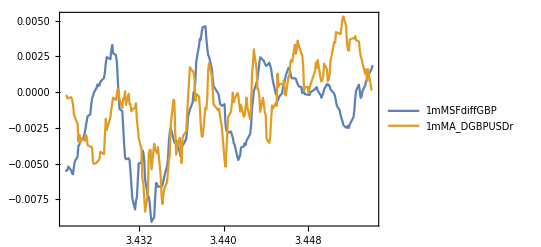

```mathematica
DateListPlot[{MSF1,mMAGBPUSDr},PlotRange->All,PlotLegends->{"1mMSFdiffGBP","1mMA_DGBPUSDr"}]
```

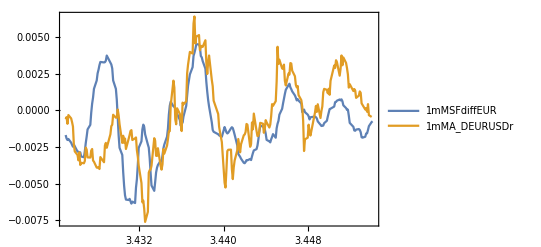

```mathematica
DateListPlot[{MSF2,mMAEURUSDr},PlotRange->All,PlotLegends->{"1mMSFdiffEUR","1mMA_DEURUSDr"}]
```

Use Variance Gamma process to fit the detrended log return L_t. Obtain three different parameters θ, m, σ.

```mathematica
NSolve[m+theta==Mean[L1]&&sigma^2+theta^2==Variance[L1]&&(2*theta^3+3sigma^2*theta)/(sigma^2+theta^2)^1.5==Skewness[L1]&&sigma>0,{m,theta,sigma},Reals]
NSolve[m+theta==Mean[L2]&&sigma^2+theta^2==Variance[L2]&&(2*theta^3+3sigma^2*theta)/(sigma^2+theta^2)^1.5==Skewness[L2]&&sigma>0,{m,theta,sigma},Reals]
```

{{theta→-0.0337078,sigma→1.28474,m→-0.205889}}

{{theta→0.159564,sigma→1.1354,m→-0.313547}}

```mathematica
Subscript[θ, 1]=-0.03370781958090384;
Subscript[m, 1]=-0.20588868196958454;
Subscript[σ, 1]=1.2847403967258448;
Subscript[θ, 2]=0.159564146305454;
Subscript[m, 2]=-0.3135466299913887;
Subscript[σ, 2]=1.135402333985649;
```

Base on Density function equation of the variance gamma process, we can see how the variance gamma process fit the empirical data.

```mathematica
F=Function[x,((2*Exp[Subscript[θ, 1]*(x-Subscript[m, 1])/Subscript[σ, 1]^2])/(Subscript[σ, 1]*Sqrt[2*Pi]*Gamma[1]))*((x-Subscript[m, 1])^2/(2*Subscript[σ, 1]^2+Subscript[θ, 1]^2))^0.25*BesselK[0.5,Sqrt[(x-Subscript[m, 1])^2*(2*Subscript[σ, 1]^2+Subscript[θ, 1]^2)]/Subscript[σ, 1]^2]][x]
```

0.550294 ⅇ^(-0.0204221 (0.205889+x)-1.10097 √((0.205889+x)^2)) (1+0./(√((0.205889+x)^2)))

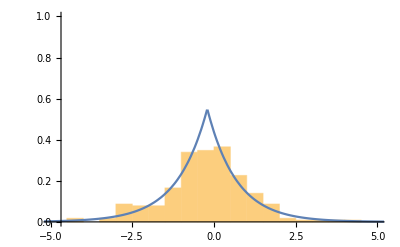

```mathematica
Show[Histogram[L1,Automatic,"ProbabilityDensity"],Plot[F,{x,-10,10},PlotRange->{Full,Full}],PlotRange->{{-5,5},{0,1}}]
```

```mathematica
G=Function[x,((2*Exp[(Subscript[θ, 2])*(x-Subscript[m, 2])/Subscript[σ, 2]^2])/(Subscript[σ, 2]*Sqrt[2*Pi]*Gamma[1]))*((x-Subscript[m, 2])^2/(2*Subscript[σ, 2]^2+Subscript[θ, 2]^2))^0.25*BesselK[0.5,Sqrt[(x-Subscript[m, 2])^2*(2*Subscript[σ, 2]^2+Subscript[θ, 2]^2)]/Subscript[σ, 2]^2]][x]
```

0.619728 ⅇ^(0.123776 (0.313547+x)-1.2517 √((0.313547+x)^2)) (1+0./(√((0.313547+x)^2)))

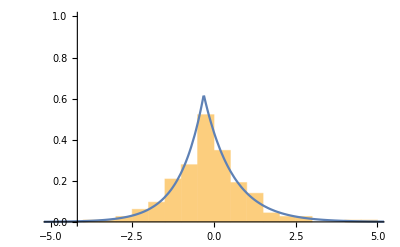

```mathematica
Show[Histogram[L2,Automatic,"ProbabilityDensity"],Plot[G,{x,-10,10},PlotRange->{Full,Full}],PlotRange->{{-5,5},{0,1}}]
```

The Chi-square test shows the variance gamma process is fit the empirical data of the detrended log return of the exchange rate.

```mathematica
𝒟1=ProbabilityDistribution[F,{x,-Infinity,Infinity}];
DistributionFitTest[L1,𝒟1,"PearsonChiSquare"]
𝒟2=ProbabilityDistribution[G,{x,-Infinity,Infinity}];
DistributionFitTest[L2,𝒟2,"PearsonChiSquare"]
```

0.487196

0.19706

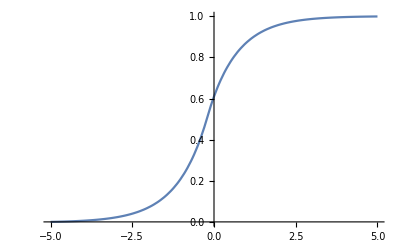

```mathematica
Plot[CDF[𝒟1,x],{x,-5,5},PlotRange->{Full,Full}]
```

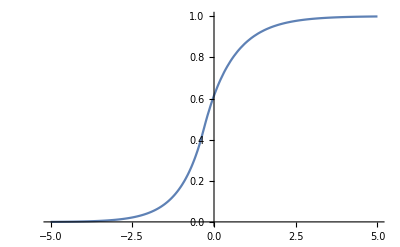

```mathematica
Plot[CDF[𝒟2,x],{x,-5,5},PlotRange->{Full,Full}]
```

We use student t copula to fit the two detrended log returns, by estimating the correlation matrix and degree of freedom.

```mathematica
Subscript[R, 1,2]=Sin[Pi*KendallTau[L1,L2]/2];
Subscript[R, 2,1]=Sin[Pi*KendallTau[L2,L1]/2]; (*Subscript[R, 1,2] = Subscript[R, 2,1]*)
R={{1,Subscript[R, 1,2]},{Subscript[R, 2,1],1}};
data=Table[{L1[[i]],L2[[i]]},{i,1,230}];
MatrixForm[R]
```

(1 | 0.677919
0.677919 | 1)

```mathematica
EstimatedDistribution[data,CopulaDistribution[{"MultivariateT",R,v},{StudentTDistribution[v],StudentTDistribution[v]}],ParameterEstimator->"MaximumLikelihood"]
```

CopulaDistribution[{MultivariateT,{{1,0.677919},{0.677919,1}},5.4015},{StudentTDistribution[5.4015],StudentTDistribution[5.4015]}]

Generate the simulation of the detrended log return L_t and the simulation of the exchange rates of EUR/USD and GBP/USD.

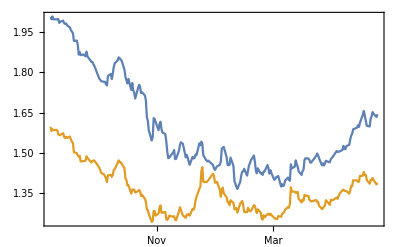

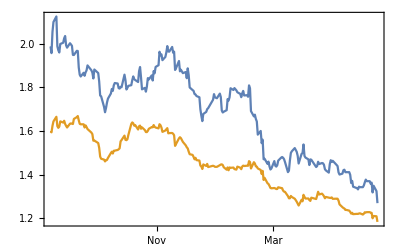

```mathematica
ν=5.401500510073012;
A=CholeskyDecomposition[R];
dist=ProductDistribution[NormalDistribution[],NormalDistribution[],ChiSquareDistribution[ν]];
z1=RandomVariate[MarginalDistribution[dist,1],230];
z2=RandomVariate[MarginalDistribution[dist,2],230];
s=RandomVariate[MarginalDistribution[dist,3],230];
For[i=1,i≤230,i++,
Subscript[s, i]=s[[i]];
Subscript[y, i]=A.{z1[[i]],z2[[i]]};
Subscript[x, i]=Sqrt[ν]/Sqrt[Subscript[s, i]]*Subscript[y, i]];
x1=Table[Subscript[x, i][[1]],{i,230}];
x2=Table[Subscript[x, i][[2]],{i,230}];
Subscript[u, 1]=CDF[StudentTDistribution[ν],x1];
Subscript[u, 2]=CDF[StudentTDistribution[ν],x2];
S1=Take[Drop[gbpusd,10],230];
S2=Take[Drop[eurusd,10],230];
Subscript[Sim1, 0]=Take[Drop[gbpusd,9],1][[1]];
Subscript[Sim2, 0]=Take[Drop[eurusd,9],1][[1]];
Subscript[L, 1]=InverseCDF[𝒟1,Subscript[u, 1]];
Subscript[L, 2]=InverseCDF[𝒟2,Subscript[u, 2]];
For[t=1,t≤230,t++,
Subscript[L, 1,t]=Subscript[L, 1][[t]];
Subscript[L, 2,t]=Subscript[L, 2][[t]];
Subscript[Sim1, t]=Subscript[Sim1, t-1]*Exp[-Subscript[k, 1]*Subscript[b1, t]+Subscript[L, 1,t]/100];
Subscript[Sim2, t]=Subscript[Sim2, t-1]*Exp[-Subscript[k, 2]*Subscript[b2, t]+Subscript[L, 2,t]/100]];
Sm1=Table[{dates[[t]],Subscript[Sim1, t]},{t,1,230}];
Sm2=Table[{dates[[t]],Subscript[Sim2, t]},{t,1,230}];
DateListPlot[{Table[{dates[[t]],S1[[t]]},{t,1,230}],Table[{dates[[t]],S2[[t]]},{t,1,230}]}]
DateListPlot[{Sm1,Sm2}]
```

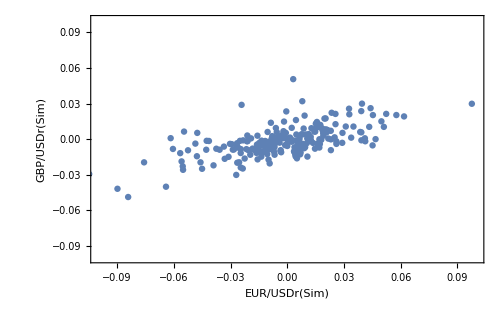

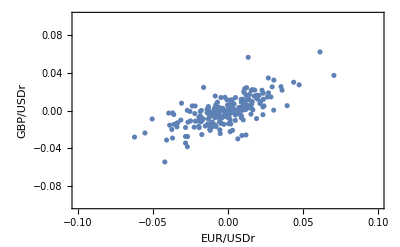

```mathematica
Sm1r=Differences[Table[Subscript[Sim1, t],{t,1,230}]];
Sm2r=Differences[Table[Subscript[Sim2, t],{t,1,230}]];
S1r=Differences[S1];
S2r=Differences[S2];
ListPlot[Table[{Sm1r[[t]],Sm2r[[t]]},{t,1,229}],Frame->True,PlotRange->{{-0.1,0.1},{-0.1,0.1}},AxesLabel->{"EUR/USDr(Sim)","GBP/USDr(Sim)"}]
ListPlot[Table[{S1r[[t]],S2r[[t]]},{t,1,229}],Frame->True,PlotRange->{{-0.1,0.1},{-0.1,0.1}},AxesLabel->{"EUR/USDr","GBP/USDr"}]
```

Scatterplot of EUR/USDr & GBP/USDr and Scatterplot of simulation of EUR/USDr & GBP/USDr

And plot the log returns and simulated log returns of EUR/USD and GBP/USD

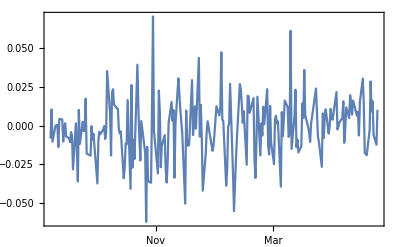

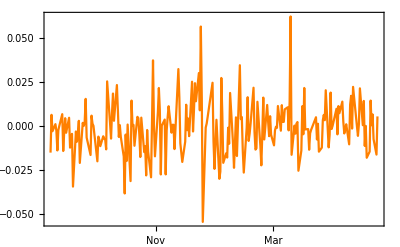

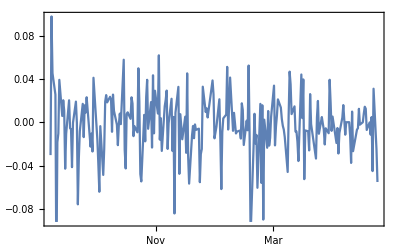

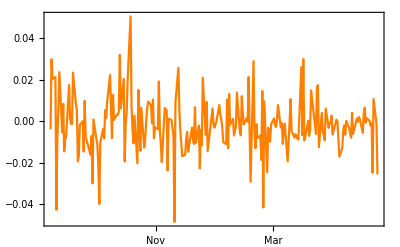

```mathematica
DateListPlot[Table[{dates[[t+1]],Differences[S1][[t]]},{t,1,229}]]
DateListPlot[Table[{dates[[t+1]],Differences[S2][[t]]},{t,1,229}],PlotStyle->Orange]
DateListPlot[Table[{dates[[t+1]],Sm1r[[t]]},{t,1,229}]]
DateListPlot[Table[{dates[[t+1]],Sm2r[[t]]},{t,1,229}],PlotStyle->Orange]
```